## Coursework 1

The following two subsections contain the examples from the initial coursework assignment sheet. The solved exercises are listed below.

# Example using Plot function

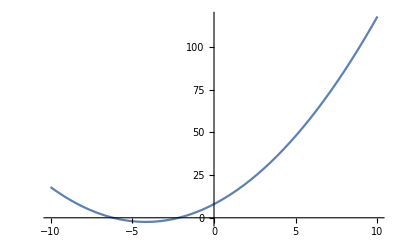

```mathematica
Plot[0.6 x^2 + 5 x + 8, {x, -10, 10}]
```

### Anti-crossing in quantum mechanics

```mathematica
symmetric2x2={{e0,v}, {v, e1}};
```

```mathematica
symmetric2x2//MatrixForm
```

(e0 | v
v | e1)

```mathematica
ham = symmetric2x2 /.{e0->x, e1->1,v->1/10};
```

```mathematica
ham // MatrixForm
```

(x | 1/10
1/10 | 1)

```mathematica
evals=Eigenvalues[ham]
```

{1/10 (5+5 x-√(26-50 x+25 x^2)),1/10 (5+5 x+√(26-50 x+25 x^2))}

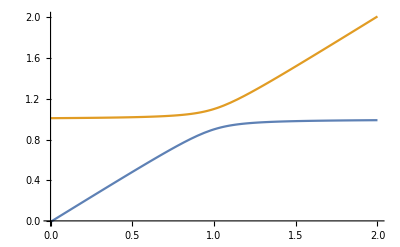

```mathematica
Plot[evals,{x,0,2}]
```

### Exercise 1: Basis state mixing

{1/10 (5+5 x-√(26-50 x+25 x^2)),1/10 (5+5 x+√(26-50 x+25 x^2))}

-Graphics-

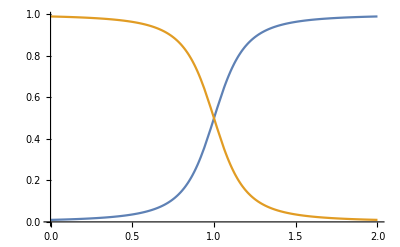

```mathematica
rules={e0->x, e1->1, v->10/100};
ham=symmetric2x2/.rules;
evals=Eigenvalues[ham]
Plot[evals,{x,0,2}]
evecs:=Eigenvectors[ham]
prob1:=Abs[Transpose[evecs][[1]]]^2;
Plot[prob1,{x,0,2}]
```

The above graph shows the evolution of the energies of the new eigenstates with x, here now referred as   and 
 and

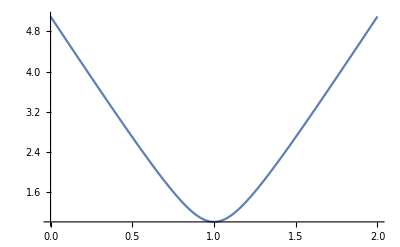

Hold[ⅇ_+]

```mathematica
Plot[√(26-50 x+25 x^2), {x,0,2}]
```